### Definitions

#### Generate Fermat-type Calabi-Yaus

```mathematica
(* compute ks *)
maxd[1]= 1;
maxd[q_]:=maxd[q]= maxd[q-1](maxd[q-1]+1)

getks[d_,q_:5]:=Reverse/@Select[IntegerPartitions[d,{q},Divisors[d]], GCD@@#==1&]
getcys[dmax_, q_:5]:=Flatten[getks[#,q]&/@Range[dmax],1]
getcysParallel[dmax_, q_:5]:=Flatten[ParallelMap[getks[#,q]&,Range[dmax]],1]

getallCYs[q_]:=If[q<=5, getcys[maxd[q],q],  getcysParallel[maxd[q],q]]
```

#### Compute the discreet Greene-Plesser group

```mathematica
(* NullSpace seems to give a correct set of group generators (before projective symmetry) if the ks are in ascending order. But more work might be required... *)
nonprojGenerators[ks_]:=NullSpace[{ks}]

(* This function tries to compute the group order for a given generator. Also needs double checking... *)
grouporder[gen_, ks_]:=Total[ks]/Min@Select[gen.DiagonalMatrix[ks],Positive]

(* Compute the discrete symmetry for a given CY. Returns the generators and the corresponding order. *)
symmetry[ks_]:=Module[{npgens,testgens,i,j},
(*Print["k=", ks, ", d=", Total[ks]];*)

(* compute generators and sort by order *)
npgens=nonprojGenerators[ks];
npgens=SortBy[{#, grouporder[#, ks]}&/@npgens,Last];

(*Print["Generators (without modding out projective symmetry): ",npgens[[All,1]]];
Print["Orders of the respective groups: ", npgens[[All,2]]];*)

(* iterate through the generators and determine whether a lin. combination with other generators is trivial when exploiting the properties of projective space (can also be trivial on its own) *)
For[i=1, i<Length[ks], i++,
testgens={npgens[[i,1]]};

(* Select other generators to test for trivial linear combinations. Select only those which are not coprime *)
For[j=i+1,j< Length[ks], j++,If[!CoprimeQ[npgens[[j,2]],npgens[[i,2]]], AppendTo[testgens, npgens[[j,1]]]]];

(*Print["i=", i, ", test generators: " , testgens];
Print["npgens: ", npgens];*)

(* Check for triviality in projective space. The output is the order of the unbroken group. *)
npgens[[i,2]]=Scan[
If[#==npgens[[i,2]]||Length[FindInstance[Thread[Join[{#},(m/@Range[Length[testgens]-1])].testgens.DiagonalMatrix[ks]-α ks==0],Join[(m/@Range[Length[testgens]-1]), {α}], Modulus->Total[ks]]]>0,Return[#]] &,
Divisors[npgens[[i,2]]]];
];

(* if a generator gives a group of order 1 its trivial -> delete *)
Select[npgens,#[[2]]!=1&]
]
```

#### Helper functions

```mathematica
(* helper functions to access parts of a vector storing Calabi-Yau data*)

(* weights of projective space *)
gks[cy_]:=cy[[1]];
(* number of weights *)
gq[cy_]:=Length[gks[cy]];
(* degree of the polynomial, i.e. the sum of the weights *)
gm[cy_]:= Total[cy[[1]]];
(* generators of a discreet symmetry *)
ggens[cy_]:=cy[[2]];
```

```mathematica
(* format stuff nicely *)

formatCP[ks_] := Subscript[ℂℙ,ks]
formatSymmetry[sym_]:=Times@@(Subscript[ℤ,#[[2]]]&/@sym)
```

```mathematica
(* compute Eigenvalues and rank of matrix numerically by assigning random numerical values to the deformation parameters and projective coordinates *)
numEigenvalues[m_,cy_]:=Eigenvalues[Normal[m]/.Join[Table[x[i]->(RandomReal[])^(gks[cy][[i]]/gm[cy]),{i,gq[cy]}],{ψ[_]->1}]]

numMatrixRank[m_,cy_,delta_:10^(-9) ]:=If[m=={{}},0,Length@Select[numEigenvalues[m,cy],Abs[#]>delta&]]
```

```mathematica
(* time and memory constrained at the same time *)
tmConstrained[expr_, time_, mem_, failexpr_]:=TimeConstrained[MemoryConstrained[expr,mem,failexpr],time,failexpr]
```

#### Generate a list of independent monomials

```mathematica
(* compute the Fermat polynomial *)
fermat[cy_]:= Sum[x[i]^(gm[cy]/gks[cy][[i]]),{i, gq[cy]}]

(* compute the Jacobi ideal for a given polynomial *)
jacobiIdeal[p_]:=D[p, {Variables[p]}]
```

```mathematica
(* generate a list of rules which implement moding out by the Jacobi ideal *)
generateJacobiRules[j_,cy_]:=Module[{i, rhs,xx,p},
Flatten@Table[
p=gm[cy]/gks[cy][[i]]-1;
rhs = First@SolveValues[0==j[[i]]/.{x[i]^p->xx},xx];
Join[{ x[i]^ToExpression["r_/;r>="<>ToString[p]]->x[i]^(r-p)rhs},If[p==1,{x[i]->rhs},{} ]],
{i,gq[cy]}]
]
```

```mathematica
(* reduce a list of monomials to a list of independent ones with respect to the Jacobi ideal around the fermat points.
Notice, that this also yields a suitable basis of monomials even when not working at the Fermat point.
 *)
indepPolys[ps_, cy_]:=Module[{rules},
rules = generateJacobiRules[jacobiIdeal[fermat[cy]],cy];
DeleteDuplicates[Select[ps/.rules,#=!=0&]]
]
```

```mathematica
(* Generate a "raw" list of monomials. This does not take the Jacobi ideal into account yet. *)
generateMonomialsRaw[cy_]:=Flatten[Table@@Join[{If[((gm[cy]-(i/@Range[2,gq[cy]]).Rest[gks[cy]])/gks[cy][[1]])∈Integers,{x[1]^((gm[cy]-(i/@Range[2,gq[cy]]).Rest[gks[cy]])/gks[cy][[1]])Product[x[j]^i[j],{j,2,gq[cy]}]},{}]},Table[{i[j],0,(gm[cy]-(i/@Range[j+1,gq[cy]]).gks[cy][[j+1;;gq[cy]]])/gks[cy][[j]]},{j,gq[cy],2,-1}]],gq[cy]-1]

(* generate a list of monomials and mod out by the Jacobi ideal. Gives a basis of polynomials complex structure deformations *)
generateMonomials[cy_]:=
indepPolys[generateMonomialsRaw[cy], cy]
```

#### Check polynomials for invariance with respect to the GP group

```mathematica
(* check whether a given polynomial is invariant with respect to the GP group of a given CY *)
invariantQMonom[m_,cy_]:=Apply[And,Map[Mod[Sum[Exponent[m,x[i]]gks[cy][[i]]#[[1,i]],{i,gq[cy]}],Total[gks[cy]]]===0&,ggens[cy]]]

invariantQ[p_,cy_]:=Apply[And,invariantQMonom[#,cy]&/@MonomialList[p]]

(* check whether a Polynomial is invariant under the GP group and not in the Jacobi ideal. If both are satisfied the polynomial itself mod the Jacobi ideal is returned, otherwise 0. *)
(*goodPolynomial[p_, jrules_, cy_]:=Module[{poly},
poly=p/.jrules;
If[poly==0, Return[0]];
If[invariantQ[poly, cy], poly,0]
]*)

goodPolynomial[p_, jrules_, cy_]:=If[invariantQMonom[p, cy], p/.jrules,0]

(* generate the mass matrix for a set of polynomial deformations ps *)
generateMassMatrix[ps_, cy_,p_:0]:=Module[{jrules},
jrules=generateJacobiRules[jacobiIdeal[If[p===0,fermat[cy],p]],cy];

SymmetrizedArray[Flatten@Table[{i,j}->goodPolynomial[ps[[i]]ps[[j]], jrules, cy],{i,Length[ps]},{j,i,Length[ps]}],{Length[ps],Length[ps]},Symmetric[{1,2}]]
]
```

#### Compute CY data

```mathematica
(* compute invariant and non-invariant deformations for a given Calabi-Yau, as well as the mass matrix for the non-invariant ones. *)
Options[computeCYdata] ={maxMassDim->Infinity, maxDeformations->Infinity, massMemoryConstraint->Infinity, checkNonPoly->False};

computeCYdata::mem ="Exceeded memory constraint (`1` bytes) for CY `2`.";

computeCYdata[cy_, OptionsPattern[]]:=Module[{inv,noninv,mass,hodgenumber,t},
(* compute a basis of monomials (modulo Jacobi ideal) *)
t=First@AbsoluteTiming[noninv=generateMonomials[cy]];
(*Print["generating monomials: ", t];*)

(* nothing more to do if there's no GP group *)
If[Length[ggens[cy]]==0,Return[{noninv,{},{{}}}]];

(* otherwise, filter for invariant and non-invariant monomials *)
t=First@AbsoluteTiming[inv =Select[noninv,OperatorApplied[invariantQ][cy]];
noninv = Complement[noninv,inv];];
(*Print["filtering monomials: ", t];*)

If[OptionValue[checkNonPoly],
hodgenumber = LGhodgenumbers[cy,1,1][[1,1]]];

(* compute the mass matrix for the non-invariant moduli
(at a locus in the invariant moduli space labeled by ψ[i]) *)
t=First@AbsoluteTiming[
mass = If[Length[noninv]<=OptionValue[maxMassDim]&&(!OptionValue[checkNonPoly] || hodgenumber==Length[inv]+Length[noninv]),
MemoryConstrained[
generateMassMatrix[noninv,cy,fermat[cy]+Sum[ψ[i]inv[[i]],{i, Min[Length[inv], OptionValue[maxDeformations]]}]],
OptionValue[massMemoryConstraint],Message[computeCYdata::mem ,OptionValue[massMemoryConstraint],gks[cy]];{{}}],
{{}}
];
];
(*Print["generating mass matrix: ", t];*)

{inv,noninv,mass}
]
```

#### Landau-Ginzburg Formula

```mathematica
(* the two products that appear in the Landau-Ginzburg formula. The first one contributes to twisted (l>0) and untwisted (l=0) sectors, the second one only to the twisted ones *)
prod1[k_,m_,x_,y_]:=(1-(x*y)^(m-k))/(1-(x*y)^k);
prod2[k_,m_,l_,x_,y_]:=(x*y)^(m/2-k)*(x/y)^(m*(Mod[l*k/m,1]-1/2));

(* the Landau-Ginzburg trace-formulate *)
LGtrace[cy_, x_, y_, maxl_:Infinity]:=Sum[
Product[
If[Mod[l*gks[cy][[i]]/gm[cy],1]==0,
prod1[gks[cy][[i]],gm[cy],x,y],
prod2[gks[cy][[i]],gm[cy],l,x,y]
],
{i,gq[cy]}
],
{l,0,Min[gm[cy]-1, maxl]}
]

(* extract the Hodge numbers h^(1,n) from the trace *)
LGhodgenumbers[cy_, maxp_:Infinity, maxq_:Infinity,maxl_:Infinity]:=Module[{tr},
tr=LGtrace[cy,x,y, maxl];
tr=Assuming[{x>0,y>0},Series[tr,{x,0,gm[cy]Min[maxp,gq[cy]-3]},{x,0,gm[cy]Min[maxq,gq[cy]-2]}]];
Table[Coefficient[tr,x^(p gm[cy])y^(q gm[cy])],{p,Min[maxp,gq[cy]-4]},{q,Min[maxq,gq[cy]-3]}]
]

mirror[hn_]:=Reverse/@hn
```

### Examples

```mathematica
(* compute all Fermat two-folds (i.e. K3s) *)
cys2=getallCYs[4];
AbsoluteTiming[cys2 =Map[{#, symmetry[#]}&,cys2];Length[cys2]]
```

{0.101614,14}

```mathematica
(* compute all Fermat three-folds CYs *)
cys3=getallCYs[5];
AbsoluteTiming[cys3 =Map[{#, symmetry[#]}&,cys3];Length[cys3]]
```

{0.764754,147}

```mathematica
(* compute all Fermat four-folds CYs *)
cys4=getallCYs[6];
AbsoluteTiming[cys4 =ParallelMap[{#, symmetry[#]}&,cys4];Length[cys4]]
```

{4.10443,3462}

```mathematica
(* print the discrete symmetry and number of invariant + non-invariant moduli for quartic, quintic, and sectic *)
{quartic, quintic, sextic} = First/@{cys2, cys3, cys4};
Grid[{formatCP[#[[1]]], formatSymmetry[#[[2]]], Length/@computeCYdata[#, maxMassDim->0][[{1,2}]]}&/@%]
```

ℂℙ_{1,1,1,1} | ℤ_4^2 | {1,18}
ℂℙ_{1,1,1,1,1} | ℤ_5^3 | {1,100}
ℂℙ_{1,1,1,1,1,1} | ℤ_6^4 | {1,425}

ℂℙ_{1,1,1,1} | ℤ_4^2 | {1,18}
ℂℙ_{1,1,1,1,1} | ℤ_5^3 | {1,100}
ℂℙ_{1,1,1,1,1,1} | ℤ_6^4 | {1,425}

```mathematica
(* another 3-fold example *)
{inv,noninv,mass}=computeCYdata[cys3[[18]]];
Grid[{{formatCP[cys3[[18,1]]], formatSymmetry[cys3[[18,2]]],Length/@{inv,noninv}}}]
```

ℂℙ_{1,1,1,6,9} | ℤ_6 ℤ_18 | {2,270}

```mathematica
(* compare with Landau-Ginzburg formula *)
LGhodgenumbers[cys3[[18]]]
```

{{272,2}}

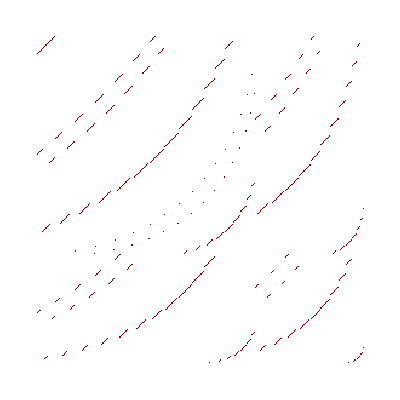

```mathematica
(* plot the (fermionic) mass matrix Subscript[D, i] Subscript[D, j] W *)
ArrayPlot[mass]
```

```mathematica
(* and compute its rank *)
MatrixRank[mass]
```

207

```mathematica
(* another 4-fold example *)
{inv,noninv,mass}=computeCYdata[cys4[[29]], maxMassDim->0];
Grid[{{formatCP[cys4[[29,1]]], formatSymmetry[cys4[[29,2]]],Length/@{inv,noninv}}}]
```

ℂℙ_{1,1,1,1,8,12} | ℤ_6 ℤ_24^2 | {2,3876}

ℂℙ_{1,1,1,1,8,12} | ℤ_6 ℤ_24^2 | {2,3876}

```mathematica
(* compare with Landau-Ginzburg formula *)
mirror@LGhodgenumbers[cys4[[29]]]
```

{{2,0,3878},{0,15564,0}}

```mathematica
(* computing the mass matrix takes quite a bit of time*)
AbsoluteTiming[mass = Last@computeCYdata[cys4[[29]]];ByteCount[mass]]
```

{515.205,4676584}

```mathematica
(* determine its rank numerically *)
numMatrixRank[mass,cys4[[29]]]
```

2824

```mathematica
(* same at the Fermat point *)
numMatrixRank[Normal@mass/.{ψ[_]->0},cys4[[29]]]
```

1956

### Compute CY-data systematically

```mathematica
AbsoluteTiming[cydata3 = ParallelMap[
Module[{inv,noninv,mass,hodgenumbers, t,r},
{inv,noninv,mass}=computeCYdata[#];
hodgenumbers = LGhodgenumbers[#];
{#[[1]],#[[2]], {Length[inv], Length[noninv]},hodgenumbers,{numMatrixRank[Normal[mass]/.{ψ[_]->0},#], numMatrixRank[mass,#]}}
]&,
cys3, Method->"FinestGrained"];]
```

{20.3004,Null}

```mathematica
cydata3[[1]]
```

{{1,1,1,1,1},{{{-1,0,0,1,0},5},{{-1,0,1,0,0},5},{{-1,1,0,0,0},5}},{1,100},{{101,1}},{50,100}}

```mathematica
AbsoluteTiming[cydata4 = ParallelMap[
tmConstrained[
Module[{inv,noninv,mass,r1,r2,t0,t1,t2,m1,m2},

{t0,{inv,noninv,mass}}=AbsoluteTiming@computeCYdata[#, maxMassDim->5000,(* maxDeformations->5,*)massMemoryConstraint->8000000000, checkNonPoly->True];

m1=ByteCount[mass];

{r1,r2}={0,0};
m2 = MaxMemoryUsed[
MemoryConstrained[
{t1,r1} = AbsoluteTiming@numMatrixRank[Normal[mass]/.{ψ[_]->0},#],8000000000];

MemoryConstrained[
{t2,r2} =AbsoluteTiming@numMatrixRank[mass,#],8000000000];
];

{#[[1]],#[[2]], {Length[inv], Length[noninv]},{r1,r2},{t0,t1,t2},{m1,m2}}
],
30*60, 16000000000, {#[[1]],#[[2]],{0,0},{0,0},{0,0,0}}]&,
cys4[[1;;3000]], Method->"FinestGrained"];]
```

```mathematica
Put[cydata4,FileNameJoin[{NotebookDirectory[], "cydataAll.txt"}]]
```

```mathematica
cydata = Get[FileNameJoin[{NotebookDirectory[], "cydata220908.txt"}]];
```

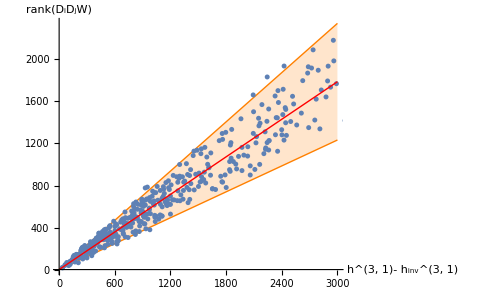

```mathematica
Show[Plot[{0.411x,0.781x},{x,0,3000}, Filling->{1->{2}}, PlotStyle->{ {Orange,Thin}, {Orange,Thin}}, AxesLabel->{"h^(3, 1)- h_inv^(3, 1)", "rank(D_iD_jW)"}],ListPlot[{#[[3,2]],#[[4,2]]}&/@cydata4c, PlotRange->Full],Plot[0.596x,{x,0,3000}, PlotStyle->{Red,Thick}]]
```

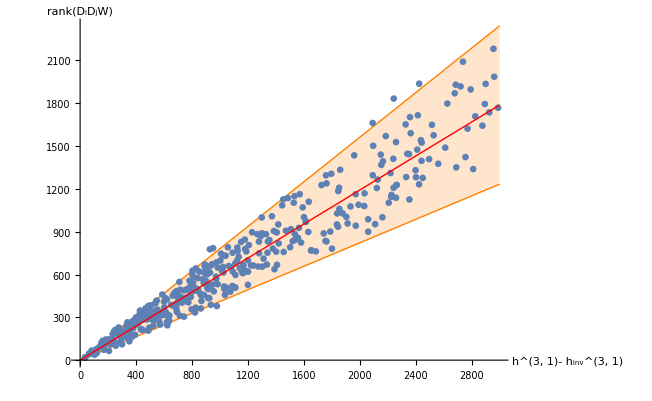

```mathematica
Show[Plot[{0.411x,0.781x},{x,0,3000}, Filling->{1->{2}}, PlotStyle->{ {Orange,Thin}, {Orange,Thin}}, AxesLabel->{"h^(3, 1)- h_inv^(3, 1)", "rank(D_iD_jW)"}],ListPlot[{#[[3,2]],#[[4,2]]}&/@cydata4c, PlotRange->Full],Plot[0.596x,{x,0,3000}, PlotStyle->{Red,Thick}]]
```